```mathematica
Needs["NDSolve`FEM`"];
```

```mathematica
Clear[torsionConstant]
torsionConstant[mesh_?MeshRegionQ]:=torsionConstant[ToElementMesh[mesh]];
torsionConstant[mesh_ElementMesh]:=Module[
{ψ,u,y,z},
ψ=NDSolveValue[{
Laplacian[u[y,z],{y,z}]==-2,
DirichletCondition[u[y,z]==0,True]
},u,{y,z}∈mesh];
2NIntegrate[ψ[y,z],{y,z}∈mesh]
]
```

```mathematica
Clear[crossSection]
crossSection[region:_?RegionQ,units_:"mm"]:=Module[
{mesh,data,A,yt,zt,y,z,colors,w,h},
(* Convert to mesh *)
mesh = ToElementMesh[region];

data={{"Measure","Value","Units"}};

(* Area *)
A=Area[mesh];
AppendTo[data,{"A",A,units^2}];

(* Mass center *)
{yt,zt}=NIntegrate[{y,z},{y,z}∈mesh]/A;

(* Bounds *)
{w,h}=(#[[2]]-#[[1]])&/@RegionBounds[mesh];

(* Moment of inertia *)
AppendTo[data,{"I_y_t",NIntegrate[(y-yt)^2,{y,z}∈mesh],units^4}];
AppendTo[data,{"I_z_t",NIntegrate[(z-zt)^2,{y,z}∈mesh],units^4}];
AppendTo[data,{"I_y_t",NIntegrate[(y-yt)(z-zt),{y,z}∈mesh],units^4}];
AppendTo[data,{"I_x_t",NIntegrate[(y-yt)^2+(z-zt)^2,{y,z}∈mesh],units^4}];
AppendTo[data,{"J_t",torsionConstant[mesh],units^4}];

(* Visualize *)
colors=ColorData[97,"ColorList"];
Grid[{{
Grid[data,Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{RGBColor["#bfbfbf"],None},{RGBColor["#f2f2f2"],None}}],
Show[
RegionPlot[mesh,AxesLabel->{"y","z"}],
Graphics[{
{Arrow[{{yt-(w+h)/10,zt},{yt+(w+h)/10,zt}}]},
{Arrow[{{yt,zt-(w+h)/10},{yt,zt+(w+h)/10}}]},
{Text[Style["y_t",FontSize->14],{yt+(w+h)/7.7,zt}]},
{Text[Style["z_t",FontSize->14],{yt,zt+(w+h)/7.7}]},
{PointSize[0.03],Point[{yt,zt}]}
}]
]
}}]
]
```

```mathematica
Ω=Disk[{0,0},1];
```

```mathematica
crossSection[Ω]
```

Area::reg: ElementMesh[{{1.,0.},{0.991575,0.129537},{0.964662,0.263492},{0.919752,0.3925},«44»,{-0.0426296,-0.811515},{0.811515,-0.0426296},«1007»},«2»,{PointElement[{{1},«49»,«46»},{«1»}]}] is not a correctly specified region.

RegionBounds::reg: ElementMesh[{{1.,0.},{0.991575,0.129537},{0.964662,0.263492},{0.919752,0.3925},«44»,{-0.0426296,-0.811515},{0.811515,-0.0426296},«1007»},«2»,{PointElement[{{1},«49»,«46»},{«1»}]}] is not a correctly specified region.

Thread::tdlen: Objects of unequal length in {TriangleElement[{{66,117,94,278,279,280},{21,22,112,281,282,283},{98,121,97,284,285,286},{111,260,134,287,288,289},{137,139,107,290,291,292},{100,123,99,293,294,295},«39»,{9,10,115,397,398,399},{33,107,32,400,401,402},{94,117,93,279,403,404},{75,86,58,405,406,407},{130,105,258,408,409,410},«454»}]}+{«1»} cannot be combined.

RegionBounds::reg: {TriangleElement[{{66,117,94,278,279,280},{21,22,112,281,282,283},{98,121,97,284,285,286},{111,260,134,287,288,289},{137,139,107,290,291,292},{100,123,99,293,294,295},«39»,{9,10,115,397,398,399},{33,107,32,400,401,402},{94,117,93,279,403,404},{75,86,58,405,406,407},{130,105,258,408,409,410},«454»}]}+{«1»} is not a correctly specified region.

Set::shape: Lists {w$86712,h$86712} and RegionBounds[{TriangleElement[{{66,117,94,278,279,280},{21,22,112,281,282,283},{98,121,97,284,285,286},{111,260,134,287,288,289},{137,139,107,290,291,292},{100,123,99,293,294,295},«40»,{33,107,32,400,401,402},{94,117,93,279,403,404},{75,86,58,405,406,407},{130,105,258,408,409,410},«454»}]}+{«1»,«50»}] are not the same shape.

Measure | Value | Units
A | Area[ElementMesh[{{-1.,1.},{-1.,1.}},{TriangleElement[<504>]}]] | mm^2
I_y_t | NIntegrate[(y$86712-yt$86712)^2,{y$86712,z$86712}∈mesh$86712] | mm^4
I_z_t | NIntegrate[(z$86712-zt$86712)^2,{y$86712,z$86712}∈mesh$86712] | mm^4
I_y_t | NIntegrate[(y$86712-yt$86712) (z$86712-zt$86712),{y$86712,z$86712}∈mesh$86712] | mm^4
I_x_t | NIntegrate[(y$86712-yt$86712)^2+(z$86712-zt$86712)^2,{y$86712,z$86712}∈mesh$86712] | mm^4
J_t | 1.57081 | mm^4 | -Graphics-

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

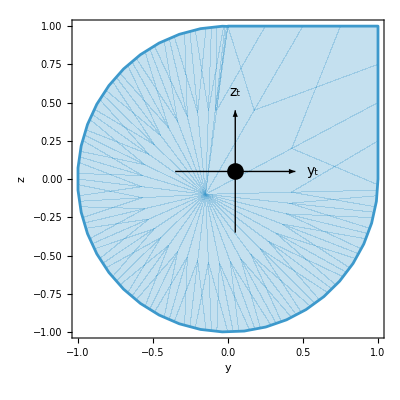
Measure | Value | Units
A | 1/4 (4+3 π) | mm^2
I_y_t | 0.914105 | mm^4
I_z_t | 0.914105 | mm^4
I_y_t | 0.116723 | mm^4
I_x_t | 1.82821 | mm^4
J_t | 1.73153 | mm^4 | -Graphics-

```mathematica
RegionUnion[Disk[{0,0},1],Rectangle[{0,0},{1,1}]];
crossSection[Ω2]
```